```mathematica
CirclInterArea[{r1_, x1_, y1_}, { r2_, x2_, y2_}] := Module[{disk1, disk2, intersec},
disk1 = Disk[{x1, y1}, r1];
disk2 = Disk[{x2, y2}, r2];
intersec = RegionIntersection[disk1, disk2];
Return[N@Area[intersec]]
]
```

```mathematica
CirclInterArea[{1, 0, 0 }, {2, 1, -1}] (*two circles*)
```

2.55607

```mathematica
Manipulate[{RegionPlot[{Disk[{x1, y1}, r1], Disk[{x2, y2}, r2]}, PlotRange->{{-7, 7}, {-7, 7}}], CirclInterArea[{r1, x1, y1}, {r2, x2, y2}]},
 {{r1, 1}, 0, 5}, {{r2, 1}, 0, 5},{{x1, 0}, -5, 5},{{x2, 0}, -5, 5},{{y1, 0}, -5, 5},{{y2, 0}, -5, 5}]
```

```mathematica
RowCircInter[{r1_, x1_, y1_}, {r2_, d_}] := Module[{xBeg = Floor[x1, d], xMin, xMax, CircTable, pipeCircl},
xMin = xBeg - (Mod[d, r1])*d;
xMax = xBeg +(Mod[r1, d]) * d;
CircTable = Table[Disk[{x, 0}, r2], {x, xMin, xMax, d}];
pipeCircl = Disk[{x1, y1}, r1];
Area@RegionIntersection[RegionUnion@CircTable,pipeCircl ]
]
```

```mathematica
Manipulate[RowCircInter[{2, x, 0.5}, {2, 5}], {x, -100, 100}]
```

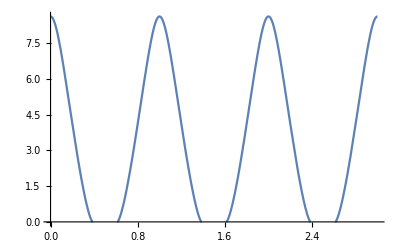

```mathematica
Plot[RowCircInter[{2, 10t, 1}, {2, 10}], {t, 0, 3}]
```

```mathematica
Play[RowCircInter[{2, 1000t, 1}, {2, 10}], {t, 0, 3}]
```

$Aborted